```mathematica
rule={u->{0,1},
d->{0,-1},
l->{-1,0},
r->{1,0}}
```

{u→{0,1},d→{0,-1},l→{-1,0},r→{1,0}}

```mathematica
Loop[x_,n_]:=Table[x,{n}]//Flatten
```

```mathematica
Pro[x__]:=Graphics@Line@Accumulate[({{x}/.List->Sequence}/.rule)]
```

```mathematica
{5{u ,l, r},r,u,r,u}/.List[n__] a_Integer->Loop[{n},a]/.Times->List//Flatten[#]&
```

Table::iterb: Iterator {a} does not have appropriate bounds.

{5,u,5,l,5,r,r,u,r,u}

```mathematica
{a l u,a l u,a l u,a l u,a l u}/.Times-> List
```

{{a,l,u},{a,l,u},{a,l,u},{a,l,u},{a,l,u}}

```mathematica
{a l u,a l u,a l u,a l u,a l u}//FullForm
```

List[Times[a,l,u],Times[a,l,u],Times[a,l,u],Times[a,l,u],Times[a,l,u]]

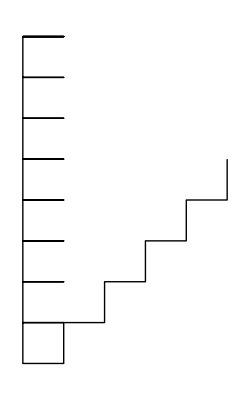

```mathematica
Pro[u,r,l,r,l,d,Loop[{r,l,d},7],Loop[{r,u},5]]
```

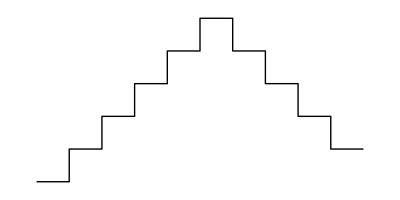

```mathematica
Pro[Loop[{u,r},5],u,r,Loop[{d,r},4]]
```

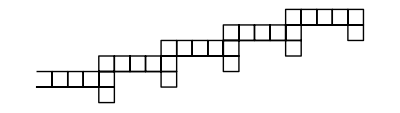

```mathematica
Pro[{Loop[{Loop[{u,r,d,l,r},5],d,l,u,u},5]}]
```

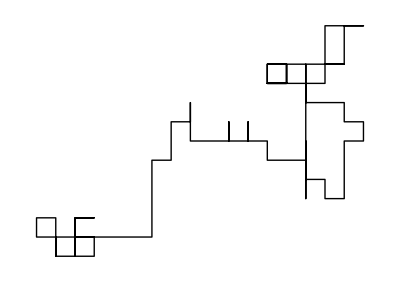

```mathematica
RandomChoice[{r,l,d,u},100]//Pro
```

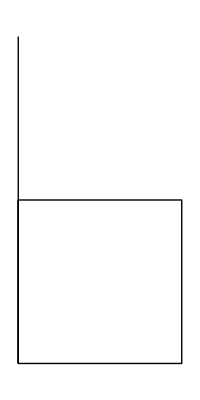

```mathematica
Pro[u,u,r,d,l,u,u]
```

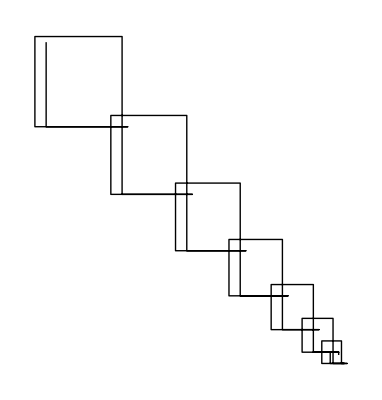

```mathematica
Loop[Sequence@@#]&/@({{u,#+1},{l,#+2},{d,#+3},{r,#+4},{l,#},{u,#+1}}&/@Range[1,30,4]//Flatten[#,1]&)//Pro
```

```mathematica
Range[1,10,4]
```

{1,5,9}

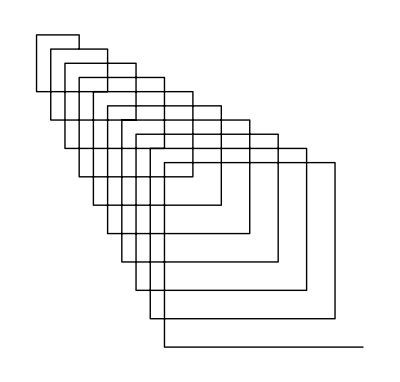

```mathematica
{{u,u},{l,l,l},{d,d,d,d},{r,r,r,r,r},{u,u,u},{l,l,l,l},{d,d,d,d,d},{r,r,r,r,r,r},{u,u,u,u},{l,l,l,l,l},{d,d,d,d,d,d},{r,r,r,r,r,r,r},{u,u,u,u,u},{l,l,l,l,l,l},{d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r},{u,u,u,u,u,u},{l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r,r,r}}//Pro
```

```mathematica
Loop[Sequence@@#]&/@{{u,1},{l,1},{d,1},{r,1},{u,1},{l,1},{d,1},{r,1},{u,2},{l,2},{d,2},{r,2},{u,3},{l,3},{d,3},{r,3},{u,5},{l,5},{d,5},{r,5},{u,8},{l,8},{d,8},{r,8},{u,13},{l,13},{d,13},{r,13},{u,21},{l,21},{d,21},{r,21},{u,34},{l,34},{d,34},{r,34},{u,55},{l,55},{d,55},{r,55}}
```

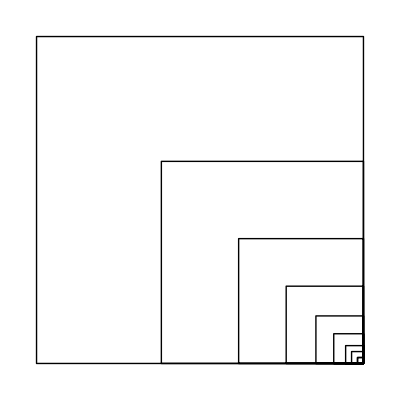

```mathematica
{{u},{l},{d},{r},{u},{l},{d},{r},{u,u},{l,l},{d,d},{r,r},{u,u,u},{l,l,l},{d,d,d},{r,r,r},{u,u,u,u,u},{l,l,l,l,l},{d,d,d,d,d},{r,r,r,r,r},{u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r}}//Pro
```

```mathematica
Loop[Sequence@@#]&/@{{u,1},{l,1},{d,1},{r,1},{u,2},{l,2},{d,2},{r,2},{u,3},{l,3},{d,3},{r,3},{u,4},{l,4},{d,4},{r,4},{u,5},{l,5},{d,5},{r,5},{u,6},{l,6},{d,6},{r,6},{u,7},{l,7},{d,7},{r,7},{u,8},{l,8},{d,8},{r,8},{u,9},{l,9},{d,9},{r,9},{u,10},{l,10},{d,10},{r,10}}
```

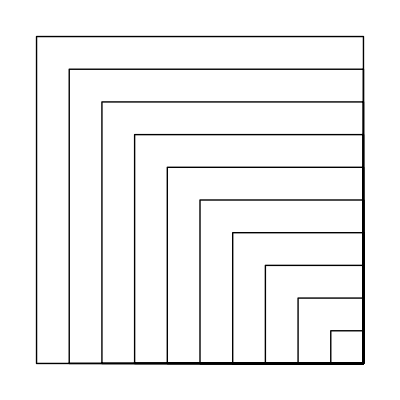

```mathematica
{{u},{l},{d},{r},{u,u},{l,l},{d,d},{r,r},{u,u,u},{l,l,l},{d,d,d},{r,r,r},{u,u,u,u},{l,l,l,l},{d,d,d,d},{r,r,r,r},{u,u,u,u,u},{l,l,l,l,l},{d,d,d,d,d},{r,r,r,r,r},{u,u,u,u,u,u},{l,l,l,l,l,l},{d,d,d,d,d,d},{r,r,r,r,r,r},{u,u,u,u,u,u,u},{l,l,l,l,l,l,l},{d,d,d,d,d,d,d},{r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r},{u,u,u,u,u,u,u,u,u,u},{l,l,l,l,l,l,l,l,l,l},{d,d,d,d,d,d,d,d,d,d},{r,r,r,r,r,r,r,r,r,r}}//Pro
```